```mathematica
SetDirectory["~/Dropbox/Doublesex/Resistance/GeneralMetapop/build/output_files"];
allelefreq[tot_]:=Block[{w,dd,r,A,B,tottot},
If[Length[tot[[1]]]==19,
w=Table[tot[[i,2]]+.5tot[[i,3]]+.5tot[[i,5]]+tot[[i,8]]+.5tot[[i,9]]+.5tot[[i,11]]+tot[[i,14]]+.5tot[[i,15]]+.5tot[[i,17]],{i,Length[tot]}];
dd=Table[tot[[i,4]]+.5tot[[i,3]]+.5tot[[i,7]]+tot[[i,10]]+.5tot[[i,9]]+.5tot[[i,13]]+tot[[i,16]]+.5tot[[i,15]]+.5tot[[i,19]],{i,Length[tot]}];
r=Table[tot[[i,6]]+.5tot[[i,5]]+.5tot[[i,7]]+tot[[i,12]]+.5tot[[i,11]]+.5tot[[i,13]]+tot[[i,18]]+.5tot[[i,17]]+.5tot[[i,19]],{i,Length[tot]}];
A=Table[Total[tot[[i,2;;7]]]+0.5Total[tot[[i,8;;13]]],{i,Length[tot]}];
tottot=(0.1+Total[Transpose[tot[[All,2;;19]]]]),
w=Table[tot[[i,2]]+.5tot[[i,3]]+.5tot[[i,5]],{i,Length[tot]}];
dd=Table[tot[[i,4]]+.5tot[[i,3]]+.5tot[[i,7]],{i,Length[tot]}];
r=Table[tot[[i,6]]+.5tot[[i,5]]+.5tot[[i,7]],{i,Length[tot]}];
A=Table[1,{i,Length[tot]}];
tottot=(0.1+Total[Transpose[tot[[All,2;;7]]]])];
N[{w/tottot,dd/tottot,r/tottot,A/tottot,(tottot-A)/tottot}]];

index=0;
res=plots=allele={{{},{},{},{}},{{},{},{},{}}};
Do[
file="Totals"<>ToString[{0,1000}[[ii]]+index-1]<>"run"<>ToString[rr]<>".txt";
If[FileExistsQ[file],tot=Import[file,"Table"];
If[Length[tot]==1503,(*Print[{ii,index,rr}];*)
totmos=Sum[tot[[12;;1503,j]],{j,lis[[ii]]}];
AppendTo[plots[[ii,index]],Table[{tot[[ii+11,1]]/365,totmos[[ii]]},{ii,Length[totmos]}]];
x=allelefreq[tot[[12;;Length[tot]]]];
AppendTo[allele[[ii,index]],Table[{tot[[ii+11,1]]/365,x[[a,ii]]},{a,{5,3}[[ii]]},{ii,Length[totmos]}]];
AppendTo[res[[ii,index]],tot[[{12,1503}]]]]],{rr,10},{index,4},{ii,2}];
```

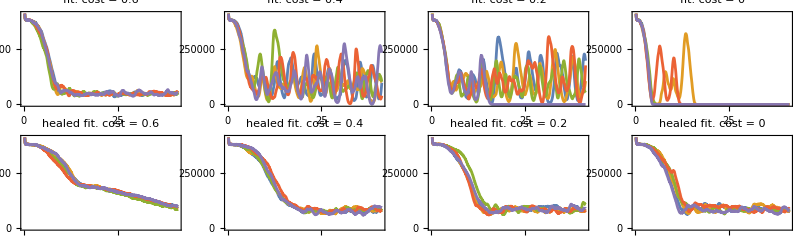

```mathematica
figtots=GraphicsGrid[Table[ListLinePlot[plots[[type,ii,1;;5]],PlotRange->All,Frame->True,PlotLabel->{"healed",""}[[type]]<>" fit. cost = "<>ToString[{0,0.2,0.4,0.6}[[ii]]]],{type,{2,1}},{ii,{4,3,2,1}}],ImageSize->800]
```

```mathematica
<<"~/Dropbox/Doublesex/FullDsxB/Colours";
cols=ColChoice["Dark2",5]
cols=ColChoice["Set1",5]
```

{RGBColor[Rational[9, 85], Rational[158, 255], Rational[7, 15]],RGBColor[Rational[217, 255], Rational[19, 51], Rational[2, 255]],RGBColor[Rational[39, 85], Rational[112, 255], Rational[179, 255]],RGBColor[Rational[77, 85], Rational[41, 255], Rational[46, 85]],RGBColor[Rational[2, 5], Rational[166, 255], Rational[2, 17]]}

{RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[11, 51], Rational[42, 85], Rational[184, 255]],RGBColor[Rational[77, 255], Rational[35, 51], Rational[74, 255]],RGBColor[Rational[152, 255], Rational[26, 85], Rational[163, 255]],RGBColor[1, Rational[127, 255], 0]}

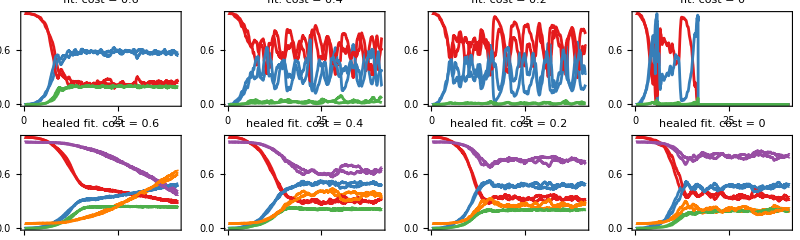

```mathematica
alleleplots=Table[Show[Table[ListLinePlot[allele[[type,fit,rep]],PlotStyle->cols,Frame->True,PlotLabel->{"healed",""}[[type]]<>" fit. cost = "<>ToString[{0,0.2,0.4,0.6}[[fit]]]],{rep,2(*Length[allele[[type,fit]]]*)}]],{type,{2,1}},{fit,{4,3,2,1}}];
fig=Legended[GraphicsGrid[alleleplots,ImageSize->800],Placed[LineLegend[cols,{"wildtype","drive","r2 allele","resident allele","healing allele"},LegendLayout->"Row"],Top]]
```

```mathematica
Export["~/Dropbox/Doublesex/Resistance/Figs/TotsPlots.pdf",figtots];
Export["~/Dropbox/Doublesex/Resistance/Figs/AllelePlots.pdf",fig];
```

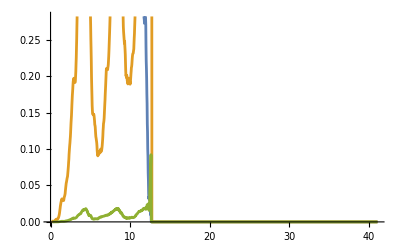

```mathematica
ListLinePlot[allele[[2,1,4]]]
```

```mathematica
lis={{2,3,5,8,9,11,14,15,17},{2,3,5}};
sup=Table[1. Total[res[[type,ii,rep,2,lis[[type]]]]]/Total[res[[type,ii,rep,1,lis[[type]]]]],{type,2},{ii,4},{rep,Length[res[[type,ii]]]}];
me=Table[Mean[sup[[type,i]]],{type,2},{i,4}]
```

{{0.198277,0.211229,0.200192,0.223935},{0.,0.231945,0.223614,0.119148}}

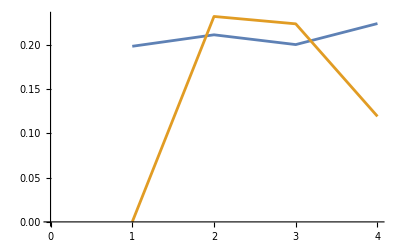

```mathematica
ListLinePlot[me,PlotRange->All,AxesOrigin->{0,0}]
```

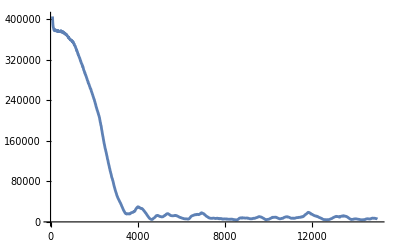

```mathematica
ListLinePlot[tot[[12;;1503,{1,2}]],PlotRange->All]
```

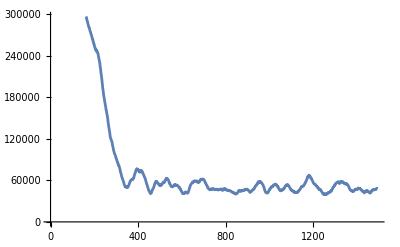

```mathematica
ListLinePlot[Sum[tot[[12;;1503,j]],{j,lis[[2]]}]]
```